```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Notebook load complete.

Notebook load complete.

```mathematica
$Assumptions=alphabar>0&&muMS>0&&s>0&&0<z1<1&&0<z2<1&&0<delta<1&&p1m>0&&p2p>0&&p1p>0&&p2m>0&&eps>0&&zerop>0

gluonSign=-1;
waveZpureDR=1(*-Cf*alphaMS*(1/eps-1/eps)/(4*Pi)*)
Z2=1+Cf*alphaMS(2/eps^2+(-2*Log[(-nu^2-I*delta)/muMS^2]+3)/eps)/(4*Pi)
Z2bar=ComplexConjugate[Z2]
hardFunc=1+alphabar(-Log[nu^2/muMS^2]^2+3Log[nu^2/muMS^2]+7zeta2-8)

keepEpsOrderMatElemSqr=2;
```

ᾱ>0∧μ_OverBar[MS]>0∧s>0∧0<z_1<1∧0<z_2<1∧0<δ<1∧p_1^->0∧p_2^+>0∧p_1^+>0∧p_2^->0∧ϵ>0∧0^+>0

1

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-ν^2-ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-ν^2+ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

ᾱ (7 ζ_2-log^2(ν^2/μ_OverBar[MS]^2)+3 log(ν^2/μ_OverBar[MS]^2)-8)+1

```mathematica
applyDiracDeltaSimplification[e_]:=Expand[e]/.a_*myDelta[z1bar]:>(Normal@Series[a,{z1,1,0},{z1bar,0,0}])*myDelta[Z1BAR]/.a_*Inactive[DiracDelta][z2bar]:>(Normal@Series[a,{z2,1,0},{z2bar,0,0}])*myDelta[Z2BAR]/.Z1BAR->z1bar/.Z2BAR->z2bar/.a_*myDelta[QT^2]:>(Normal@Series[a/.QT->Sqrt[xyz],{xyz,0,0}])*myDelta[xyz]/.a_*myDelta[QT^2-b_]:>(a/.QT->Sqrt[b])*myDelta[QT^2-b]/.xyz->QT^2/.c_*myDelta[a_*z1bar]:> (c*myDelta[z1bar]/Abs[a])/.c_*myDelta[a_*z2bar]:> (c*myDelta[z2bar]/Abs[a])

applyDiracDeltaZ1[e_]:=e/.c_*myDelta[a_*z1-b_]:> (c/a/.z1->b/a)/.c_*myDelta[a_*z1+b_]:> (c/a/.z1->-b/a)e/.c_*myDelta[a_*z1-b_]:> (c/a/.z1->b/a)
applyDiracDeltaZ2[e_]:=e/.c_*myDelta[a_*z2-b_]:> (c/a/.z2->b/a)/.c_*myDelta[a_*z2+b_]:> (c/a/.z2->-b/a)

applyDiracDeltaKMinus[e_]:=e/.b_*myDelta[km-a_]:> (b/.km->a)/.b_*myDelta[km+a_]:> (b/.km->-a)/.b_*myDelta[km]:> (b/.km->0)
applyDiracDeltaKPlus[e_]:=e/.b_*myDelta[kp-a_]:> (b/.kp->a)/.b_*myDelta[kp+a_]:> (b/.kp->-a)
applyDiracDeltaKPerp[e_]:=e/.b_*myDelta[Vperp[k]-a_]:> (b/.Vperp[k]->a)/.b_*myDelta[Vperp[k]+a_]:> (b/.Vperp[k]->-a)

applyKsqrDiracDeltaKMinus[e_]:=e/.b_*myDelta[km*c_-a_]:> (b/c/.km->a/c)/.b_*myDelta[km*c_+a_]:> (b/c/.km->-a/c)
applyKsqrDiracDeltaKPlus[e_]:=e/.b_*myDelta[kp*c_-a_]:> (b/c/.kp->a/c)/.b_*myDelta[kp*c_+a_]:> (b/c/.kp->-a/c)

applyPlusIdentity[e_]:=e/.a_^(-1-eps)/;a==km||a==kp:>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]

applyDrellYanNotation[e_]:=e/.SPD[nb,Q]->z1*p1m/.SPD[n,Q]->z2*p2p/.SPD[Vperp[Q]]->-QT^2

simplifyDeltas[e_]:=e/.myDelta[a_*b_-a_]:>myDelta[1-b]/a
```

### SCET -- when matching at Q, can assert all perps are small

#### Leading Order

```mathematica
(* qqbar->current->qqbar *)

matElemLO=(Sqrt[waveZpureDR])^2*SpinorVBar[p2].Phatn.GAD[tau].Phatn.SpinorU[p1]//DiracSimplify//FCE

matElemDagLO=(Sqrt[waveZpureDR])^2*SpinorUBar[p1].Phatnb.GAD[rho].Phatnb.SpinorV[p2]//DiracSimplify//FCE

(matElemLO/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagLO/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
spinAvg=-Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark *)

(* below, we just use k to get the kinemtics from our predefined function -- there is no actual gluon at LO *)
momConsDelta=(2Pi)^D myDelta[p1m-SPD[Q,nb]]myDelta[p2p-SPD[Q,n]]Inactive[DiracDelta][-SPD[Vperp[Q],Vperp[Q]]](4/SDM2)
(* ^ the 4 comes from a factor of 2 for the lightcone coordinates, then another factor of 2 from changing from |kT| -> kT^2 *)
(* SDM2 is the surface area of a D-2 dimensional ball *)

spinAvgWmunu=spinAvg*momConsDelta/2/Pi/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify(**(Q^2*z1bar*z2bar*muMS^2*Exp[EulerGamma]/Pi)^eps/(2*Pi)*)//applyDrellYanNotation

%/.SDM2->2*Pi^((D-2)/2)/Gamma[(D-2)/2]//Simplify
%/.D->4-2*eps//FullSimplify
Series[%,{alphaMS,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
%(*/.DiracDelta[tauPerp*a_]:>DiracDelta[tauPerp]/a*)/.z1->1-z1bar/.z2->1-z2bar/.DiracDelta[z1bar*a_]:>Inactive[DiracDelta][z1bar]/a/.DiracDelta[z2bar*a_]:>Inactive[DiracDelta][z2bar]/a/.tauPerp->QT^2/p1m/p2p

Series[%/(Z2*Z2bar)//expLogs//Expand,{alphaMS,0,1}]/.Log[-nu^2-I*delta]->2Log[nu]-I*Pi/.Log[-nu^2+I*delta]->2Log[nu]+I*Pi//Normal//Expand

forwardLO=Series[%,{eps,0,0}]//Normal
```

φ(p_2).(P̂)_n.γ^τ.(P̂)_n.φ(p_1)

φ(p_1).(P̂)_(n̄).γ^ρ.(P̂)_(n̄).φ(p_2)

(P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^ρ.(P̂)_(n̄).(γ·p_2)

-1/4 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2)+1/2 p_1^- n^τ (n̄)^ρ (γ·n).(γ·p_2)+1/4 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2)-1/2 p_1^- γ^τ.γ^ρ.(γ·n).(γ·p_2)

1/4 (-2 p_1^- (-p_2^+ g^ρτ+n^τ p_2^ρ-n^ρ p_2^τ)-2 p_2^+ p_1^- n^τ (n̄)^ρ+p_1^- n^τ (-p_2^- n^ρ+p_2^+ (n̄)^ρ+2 p_2^ρ)-p_1^- n^ρ (-p_2^- n^τ+p_2^+ (n̄)^τ+2 p_2^τ))

(2^(D+2) π^D DiracDelta[p_2^+-Q^+] DiracDelta[p_1^--Q^-] DiracDelta[-(Q_⊥)^2])/SDM2

(2^D π^(D-1) p_2^+ p_1^- (g^ρτ)_⊥ DiracDelta[p_2^+-p_2^+ z_2] DiracDelta[p_1^--p_1^- z_1] DiracDelta[Q_T^2])/SDM2

2^(D-1) π^(D/2) p_2^+ p_1^- (D-2)/2 (g^ρτ)_⊥ DiracDelta[p_2^+ (-(z_2-1))] DiracDelta[p_1^- (-(z_1-1))] DiracDelta[Q_T^2]

p_2^+ p_1^- 2^(3-2 ϵ) π^(2-ϵ) 1-ϵ (g^ρτ)_⊥ DiracDelta[p_2^+ (-(z_2-1))] DiracDelta[p_1^- (-(z_1-1))] DiracDelta[Q_T^2]

p_2^+ p_1^- 2^(3-2 ϵ) π^(2-ϵ) 1-ϵ (g^ρτ)_⊥ DiracDelta[p_2^+ (-(z_2-1))] DiracDelta[p_1^- (-(z_1-1))] DiracDelta[Q_T^2]

8 π^2 p_2^+ p_1^- (g^ρτ)_⊥ DiracDelta[p_2^+ (-(z_2-1))] DiracDelta[p_1^- (-(z_1-1))] DiracDelta[Q_T^2]

8 π^2 p_2^+ p_1^- (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]

-(8 π p_2^+ p_1^- C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ^2+(16 π p_2^+ p_1^- C_F log(ν) α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ-(12 π p_2^+ p_1^- C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ-(16 π p_2^+ p_1^- C_F α_OverBar[MS] log(μ_OverBar[MS]) (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ+8 π^2 p_2^+ p_1^- (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]

-(8 π p_2^+ p_1^- C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ^2+(16 π p_2^+ p_1^- C_F log(ν) α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]-12 π p_2^+ p_1^- C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]-16 π p_2^+ p_1^- C_F α_OverBar[MS] log(μ_OverBar[MS]) (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ+8 π^2 p_2^+ p_1^- (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]

```mathematica
forwardLO//applyDrellYanNotation//FullSimplify
WmunuAvg0g=%/.z1->1-z1bar/.z2->1-z2bar//applyDiracDeltaSimplification//FullSimplify
```

-(8 π p_2^+ p_1^- C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ^2+(16 π p_2^+ p_1^- C_F log(ν) α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]-12 π p_2^+ p_1^- C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]-16 π p_2^+ p_1^- C_F α_OverBar[MS] log(μ_OverBar[MS]) (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2])/ϵ+8 π^2 p_2^+ p_1^- (g^ρτ)_⊥ DiracDelta[(z̄)_2 p_2^+] DiracDelta[(z̄)_1 p_1^-] DiracDelta[Q_T^2]

-(8 π C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_1] DiracDelta[(z̄)_2] DiracDelta[Q_T^2])/ϵ^2+(16 π C_F log(ν) α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_1] DiracDelta[(z̄)_2] DiracDelta[Q_T^2])/ϵ-(12 π C_F α_OverBar[MS] (g^ρτ)_⊥ DiracDelta[(z̄)_1] DiracDelta[(z̄)_2] DiracDelta[Q_T^2])/ϵ-(16 π C_F α_OverBar[MS] log(μ_OverBar[MS]) (g^ρτ)_⊥ DiracDelta[(z̄)_1] DiracDelta[(z̄)_2] DiracDelta[Q_T^2])/ϵ+8 π^2 (g^ρτ)_⊥ DiracDelta[(z̄)_1] DiracDelta[(z̄)_2] DiracDelta[Q_T^2]

#### NLO setup

```mathematica
(* the (1/2) comes from the measure, the 2 comes from the dirac deltas *)

momConsDeltaN=2(1/2)myDelta[SPD[Q,n]-p2p]myDelta[SPD[Q,nb]+km-p1m]myDelta[Vperp[Q]+Vperp[k]-Vperp[p1]-Vperp[p2]]

momConsDeltaNb=2(1/2)myDelta[SPD[Q,n]+kp-p2p]myDelta[SPD[Q,nb]-p1m]myDelta[Vperp[Q]+Vperp[k]-Vperp[p1]-Vperp[p2]]

momConsDeltaOver=2(1/2)myDelta[SPD[Q,n]-p2p]myDelta[SPD[Q,nb]-p1m]myDelta[Vperp[Q]+Vperp[k]-Vperp[p1]-Vperp[p2]]
```

DiracDelta[Q^+-p_2^+] DiracDelta[k^--p_1^-+Q^-] DiracDelta[k_⊥-p_1_⊥-p_2_⊥+Q_⊥]

DiracDelta[Q^--p_1^-] DiracDelta[k^+-p_2^++Q^+] DiracDelta[k_⊥-p_1_⊥-p_2_⊥+Q_⊥]

DiracDelta[Q^+-p_2^+] DiracDelta[Q^--p_1^-] DiracDelta[k_⊥-p_1_⊥-p_2_⊥+Q_⊥]

```mathematica
(* use the delta regulator *)

matElemDagN=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]-GAD[alpha].GSD[k])/(-2SPD[p1,k])-FVD[nb,alpha](nu1)^eta1/(-SPD[nb,k]+I*zerop)^(1+eta1)).Phatnb.GAD[tau].Phatnb.SpinorV[p2]//DiracSimplify//FCE


matElemDagNbar=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.((2FVD[p2,alpha]-GSD[k].GAD[alpha])/(-2SPD[p2,k])-FVD[n,alpha](nu2)^eta2/(-SPD[n,k]+I*zerop)^(1+eta2)).SpinorV[p2]//DiracSimplify//FCE

matElemDagOver=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.(FVD[nb,alpha](nu3)^eta3/(-SPD[nb,k]+I*zerop)^(1+eta3)-FVD[n,alpha](nu4)^eta4/(-SPD[n,k]+I*zerop)^(1+eta4)).SpinorV[p2]//DiracSimplify//FCE
```

ⅈ g ν_1^η_1 (n̄)^α (-k^-+ⅈ 0^+)^(-η_1-1) φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2)+(ⅈ g p_1^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_1)-(ⅈ g φ(p_1).γ^α.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(2 k·p_1)

-ⅈ g ν_2^η_2 n^α (-k^++ⅈ 0^+)^(-η_2-1) φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2)-(ⅈ g p_2^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_2)+(ⅈ g φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.φ(p_2))/(2 k·p_2)

ⅈ g ν_3^η_3 (n̄)^α (-k^-+ⅈ 0^+)^(-η_3-1) φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2)-ⅈ g ν_4^η_4 n^α (-k^++ⅈ 0^+)^(-η_4-1) φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2)

```mathematica
matElemN=I*g*SpinorVBar[p2].Phatn.GAD[rho].Phatn.((2FVD[p1,alpha]-GSD[k].GAD[alpha])/(-2SPD[p1,k])-FVD[nb,alpha](nu1)^eta1/(-SPD[nb,k]+I*zerop)^(1+eta1)).SpinorU[p1]//DiracSimplify//FCE

matElemNbar=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]-GAD[alpha].GSD[k])/(-2SPD[p2,k])-FVD[n,alpha](nu2)^eta2/(-SPD[n,k]+I*zerop)^(1+eta2)).Phatn.GAD[rho].Phatn.SpinorU[p1]//DiracSimplify//FCE

matElemOver=-I*g*SpinorVBar[p2].(FVD[nb,alpha](nu3)^eta3/(-SPD[nb,k]+I*zerop)^(1+eta3)-FVD[n,alpha](nu4)^eta4/(-SPD[n,k]+I*zerop)^(1+eta4)).Phatn.GAD[rho].Phatn.SpinorU[p1]//DiracSimplify//FCE
```

-ⅈ g ν_1^η_1 (n̄)^α (-k^-+ⅈ 0^+)^(-η_1-1) φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1)-(ⅈ g p_1^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_1)+(ⅈ g φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·k).γ^α.φ(p_1))/(2 k·p_1)

ⅈ g ν_2^η_2 n^α (-k^++ⅈ 0^+)^(-η_2-1) φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1)+(ⅈ g p_2^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_2)-(ⅈ g φ(p_2).γ^α.(γ·k).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(2 k·p_2)

ⅈ g ν_4^η_4 n^α (-k^++ⅈ 0^+)^(-η_4-1) φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1)-ⅈ g ν_3^η_3 (n̄)^α (-k^-+ⅈ 0^+)^(-η_3-1) φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1)

#### N sector

```mathematica
gluonSign(matElemN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE;

%//PhatDef//DiracSimplify//FCE;
spinAvgN=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

traceN=%/.SPD[k,k]->0//lcCompAll;

tempN=traceN/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify

LOsectorWmunuAvgN=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal
```

-1/4 C_F (-(4 g^2 ν_1^η_1 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)+(4 g^2 ν_1^η_1 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) (p_1^-)^2 (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)+(4 g^2 ν_1^η_1 n^ρ (n̄)^τ k^- p_2^+ p_1^- (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)-(4 g^2 ν_1^η_1 k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)-(2 g^2 ν_1^η_1 n^τ (p_1^-)^2 (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)+(2 g^2 ν_1^η_1 n^τ k^- p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)+(2 g^2 ν_1^η_1 n^ρ (p_1^-)^2 (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)-(2 g^2 ν_1^η_1 n^ρ k^- p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) (ⅈ 0^+-k^-)^(-η_1-1))/(k·p_1)+(D g^2 n^ρ (n̄)^τ k^- p_2^+)/(k·p_1)-(2 g^2 n^ρ (n̄)^τ k^- p_2^+)/(k·p_1)-(D g^2 k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+))/(k·p_1)+(2 g^2 k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+))/(k·p_1)-(D g^2 n^ρ (n̄)^τ k^2 p_2^+ p_1^-)/(2 (k·p_1)^2)+(g^2 n^ρ (n̄)^τ k^2 p_2^+ p_1^-)/(k·p_1)^2+(D g^2 k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^-)/(2 (k·p_1)^2)-(g^2 k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^-)/(k·p_1)^2-(D g^2 n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(4 (k·p_1)^2)+(g^2 n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(2 (k·p_1)^2)+(D g^2 n^τ k^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(2 k·p_1)-(g^2 n^τ k^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(k·p_1)+(D g^2 n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(4 (k·p_1)^2)-(g^2 n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(2 (k·p_1)^2)-(D g^2 n^ρ k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(2 k·p_1)+(g^2 n^ρ k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(k·p_1))

(g^2 p_2^+ C_F (-k^-+ⅈ 0^+)^-η_1 (g^ρτ)_⊥ (0^+ (D-2) k^- (-k^-+ⅈ 0^+)^η_1+ⅈ ((D-2) (k^-)^2 (-k^-+ⅈ 0^+)^η_1-4 k^- p_1^- ν_1^η_1+4 (p_1^-)^2 ν_1^η_1)))/(2 (0^++ⅈ k^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥))

-(g^2 k^- p_2^+ ϵ C_F (g^ρτ)_⊥)/(2 π (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥))+(g^2 p_2^+ C_F (-k^-+ⅈ 0^+)^-η_1 (g^ρτ)_⊥ (ⅈ (k^-)^2 (-k^-+ⅈ 0^+)^η_1+0^+ k^- (-k^-+ⅈ 0^+)^η_1-2 ⅈ k^- p_1^- ν_1^η_1+2 ⅈ (p_1^-)^2 ν_1^η_1))/(2 π (0^++ⅈ k^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥))

#### Nbar sector

```mathematica
gluonSign(matElemNbar/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagNbar/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE;

%//PhatDef//DiracSimplify//FCE;
spinAvgNb=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

traceNb=%/.SPD[k,k]->0//lcCompAll;

tempNb=traceNb/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify

LOsectorWmunuAvgNbar=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal
```

-1/4 C_F (-(4 g^2 ν_2^η_2 n^ρ (n̄)^τ (p_2^+)^2 p_1^- (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)+(4 g^2 ν_2^η_2 n^ρ (n̄)^τ k^+ p_2^+ p_1^- (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)+(4 g^2 ν_2^η_2 p_2^+ (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)-(4 g^2 ν_2^η_2 k^+ (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)-(2 g^2 ν_2^η_2 n^τ p_2^+ p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)+(2 g^2 ν_2^η_2 n^τ k^+ p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)+(2 g^2 ν_2^η_2 n^ρ p_2^+ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)-(2 g^2 ν_2^η_2 n^ρ k^+ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) (ⅈ 0^+-k^+)^(-η_2-1))/(k·p_2)+(2 g^2 n^ρ (n̄)^τ p_2^+ p_1^-)/(k·p_2)-(D g^2 n^ρ (n̄)^τ k^2 p_2^+ p_1^-)/(2 (k·p_2)^2)+(2 g^2 n^ρ (n̄)^τ k^2 p_2^+ p_1^-)/(k·p_2)^2+(g^2 (n̄)^τ p_2^+ (p_2^ρ k^+-n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2+(2 g^2 k^τ (p_2^ρ k^+-n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2+(2 g^2 p_2^τ (p_2^ρ k^+-n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2+(D g^2 k^τ (p_2^ρ k^++n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2-(4 g^2 k^τ (p_2^ρ k^++n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2+(D g^2 (n̄)^τ k^+ (p_2^ρ k^++n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(2 (k·p_2)^2)-(g^2 (n̄)^τ k^+ (p_2^ρ k^++n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2-(D g^2 n^τ k^- (p_2^ρ k^++n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(2 (k·p_2)^2)+(g^2 n^τ k^- (p_2^ρ k^++n^ρ k·p_2-k^ρ p_2^+) p_1^-)/(k·p_2)^2-(g^2 (n̄)^ρ p_2^+ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2-(2 g^2 k^ρ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2-(2 g^2 p_2^ρ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2-(g^2 (n̄)^ρ k^+ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2+(g^2 n^ρ k^- (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2-(D g^2 k^ρ (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2+(4 g^2 k^ρ (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2-(D g^2 (n̄)^ρ k^+ (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^-)/(2 (k·p_2)^2)+(2 g^2 (n̄)^ρ k^+ (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2+(D g^2 n^ρ k^- (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^-)/(2 (k·p_2)^2)-(2 g^2 n^ρ k^- (p_2^τ k^++n^τ k·p_2-k^τ p_2^+) p_1^-)/(k·p_2)^2-(g^2 k^2 (n^τ p_2^ρ+n^ρ p_2^τ-g^ρτ p_2^+) p_1^-)/(k·p_2)^2-(2 g^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^-)/(k·p_2)+(D g^2 k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^-)/(2 (k·p_2)^2)-(2 g^2 k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^-)/(k·p_2)^2-(g^2 n^τ (p_2^ρ k^+-n^ρ k·p_2-k^ρ p_2^+) p_1^- p_2^-)/(k·p_2)^2+(g^2 n^ρ (p_2^τ k^+-n^τ k·p_2-k^τ p_2^+) p_1^- p_2^-)/(k·p_2)^2+(g^2 n^τ k^+ p_1^- (p_2^ρ k^--(n̄)^ρ k·p_2-k^ρ p_2^-))/(k·p_2)^2+(g^2 n^τ k^+ p_1^- (p_2^ρ k^--(n̄)^ρ k·p_2+k^ρ p_2^-))/(k·p_2)^2-(g^2 n^ρ p_2^+ p_1^- (p_2^τ k^--(n̄)^τ k·p_2-k^τ p_2^-))/(k·p_2)^2-(2 g^2 n^ρ k^+ p_1^- (p_2^τ k^--(n̄)^τ k·p_2-k^τ p_2^-))/(k·p_2)^2-(D g^2 n^ρ k^+ p_1^- (p_2^τ k^-+(n̄)^τ k·p_2-k^τ p_2^-))/(2 (k·p_2)^2)+(2 g^2 n^ρ k^+ p_1^- (p_2^τ k^-+(n̄)^τ k·p_2-k^τ p_2^-))/(k·p_2)^2-(g^2 n^ρ k^+ p_1^- (p_2^τ k^--(n̄)^τ k·p_2+k^τ p_2^-))/(k·p_2)^2+(g^2 n^τ p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(k·p_2)-(D g^2 n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(4 (k·p_2)^2)+(g^2 n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(k·p_2)^2-(g^2 n^τ k^+ k^- p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-))/(2 (k·p_2)^2)+(g^2 n^τ k^2 p_1^- (2 p_2^ρ-(n̄)^ρ p_2^++n^ρ p_2^-))/(2 (k·p_2)^2)-(g^2 n^τ k^+ k^- p_1^- (2 p_2^ρ-(n̄)^ρ p_2^++n^ρ p_2^-))/(2 (k·p_2)^2)+(g^2 n^ρ k^2 p_1^- (2 p_2^τ-(n̄)^τ p_2^+-n^τ p_2^-))/(2 (k·p_2)^2)-(g^2 n^ρ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(k·p_2)+(D g^2 n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(4 (k·p_2)^2)-(g^2 n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(k·p_2)^2+(g^2 n^ρ k^+ k^- p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-))/(2 (k·p_2)^2)+(g^2 n^ρ k^+ k^- p_1^- (2 p_2^τ-(n̄)^τ p_2^++n^τ p_2^-))/(2 (k·p_2)^2)-(g^2 n^ρ (n̄)^τ p_2^+ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(2 (k·p_2)^2)+(g^2 k^τ n^ρ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(k·p_2)^2-(g^2 k^ρ n^τ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(k·p_2)^2-(g^2 n^τ p_2^ρ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(k·p_2)^2+(g^2 n^ρ p_2^τ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(k·p_2)^2+(D g^2 n^ρ (n̄)^τ k^+ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(4 (k·p_2)^2)-(3 g^2 n^ρ (n̄)^τ k^+ p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(2 (k·p_2)^2)+(g^2 n^ρ n^τ k^- p_1^- (2 k·p_2+k^- p_2^+-k^+ p_2^-))/(2 (k·p_2)^2)-(g^2 n^ρ (n̄)^τ p_2^+ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(2 (k·p_2)^2)-(D g^2 k^τ n^ρ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(2 (k·p_2)^2)+(2 g^2 k^τ n^ρ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(k·p_2)^2+(D g^2 k^ρ n^τ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(2 (k·p_2)^2)-(2 g^2 k^ρ n^τ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(k·p_2)^2+(D g^2 n^ρ (n̄)^τ k^+ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(4 (k·p_2)^2)-(3 g^2 n^ρ (n̄)^τ k^+ p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(2 (k·p_2)^2)+(g^2 n^ρ n^τ k^- p_1^- (2 k·p_2-k^- p_2^++k^+ p_2^-))/(2 (k·p_2)^2)+(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^++k^τ n^ρ p_2^--k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)-(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ+2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^+-k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^--k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)+(g^2 k^+ p_1^- (2 k^τ p_2^ρ+(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ+2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^--k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(k·p_2)^2-(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ+n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^--k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)-(g^2 k^+ p_1^- (2 k^τ p_2^ρ+(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^+-k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^-+k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(k·p_2)^2-(g^2 p_2^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^-+k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)-(D g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^-+k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(4 (k·p_2)^2)+(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^++k^τ n^ρ p_2^-+k^ρ n^τ p_2^--g^ρτ k^+ p_2^-))/(k·p_2)^2+(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ+2 k^ρ p_2^τ-(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2+k^τ (n̄)^ρ p_2^+-k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^--k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)-(g^2 k^+ p_1^- (2 k^τ p_2^ρ+(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ+2 k^ρ p_2^τ-(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2+k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^--k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(k·p_2)^2-(g^2 p_2^+ p_1^- (2 k^τ p_2^ρ+(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ-(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2+k^τ (n̄)^ρ p_2^+-k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(k·p_2)^2-(D g^2 k^+ p_1^- (2 k^τ p_2^ρ+(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ-(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2+k^τ (n̄)^ρ p_2^+-k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)+(2 g^2 k^+ p_1^- (2 k^τ p_2^ρ+(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ-(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2+k^τ (n̄)^ρ p_2^+-k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(k·p_2)^2+(g^2 p_2^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)+(D g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(4 (k·p_2)^2)-(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^-+n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(k·p_2)^2-(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ-n^τ k^- p_2^ρ-2 k^ρ p_2^τ-(n̄)^ρ p_2^τ k^++n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2-n^ρ (n̄)^τ k·p_2+2 g^ρτ k·p_2+k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^+-g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(2 (k·p_2)^2)+(g^2 k^+ p_1^- (2 k^τ p_2^ρ-(n̄)^τ k^+ p_2^ρ+n^τ k^- p_2^ρ-2 k^ρ p_2^τ+(n̄)^ρ p_2^τ k^+-n^ρ p_2^τ k^--n^τ (n̄)^ρ k·p_2+n^ρ (n̄)^τ k·p_2-2 g^ρτ k·p_2-k^τ (n̄)^ρ p_2^++k^ρ (n̄)^τ p_2^++g^ρτ k^- p_2^+-k^τ n^ρ p_2^-+k^ρ n^τ p_2^-+g^ρτ k^+ p_2^-))/(2 (k·p_2)^2))

(g^2 p_1^- C_F (-k^++ⅈ 0^+)^-η_2 (g^ρτ)_⊥ (0^+ (D-2) k^+ (-k^++ⅈ 0^+)^η_2+ⅈ ((D-2) (k^+)^2 (-k^++ⅈ 0^+)^η_2-4 k^+ p_2^+ ν_2^η_2+4 (p_2^+)^2 ν_2^η_2)))/(2 (0^++ⅈ k^+) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))

-(g^2 k^+ p_1^- ϵ C_F (g^ρτ)_⊥)/(2 π (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+(g^2 p_1^- C_F (-k^++ⅈ 0^+)^-η_2 (g^ρτ)_⊥ (ⅈ (k^+)^2 (-k^++ⅈ 0^+)^η_2+0^+ k^+ (-k^++ⅈ 0^+)^η_2-2 ⅈ k^+ p_2^+ ν_2^η_2+2 ⅈ (p_2^+)^2 ν_2^η_2))/(2 π (0^++ⅈ k^+) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))

#### Overlap sector

```mathematica
gluonSign(matElemOver/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagOver/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE;

%//PhatDef//DiracSimplify//FCE;
spinAvgOver=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

traceOver=%/.SPD[k,k]->0//lcCompAll;

tempOver=traceOver/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify

LOsectorWmunuAvgOver=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal
```

-1/4 C_F (8 g^2 p_2^+ p_1^- ν_3^η_3 ν_4^η_4 n^ρ (n̄)^τ (-k^++ⅈ 0^+)^(-η_4-1) (-k^-+ⅈ 0^+)^(-η_3-1)+4 g^2 p_1^- ν_3^η_3 ν_4^η_4 n^τ (-k^++ⅈ 0^+)^(-η_4-1) (-k^-+ⅈ 0^+)^(-η_3-1) (-p_2^- n^ρ+p_2^+ (n̄)^ρ+2 p_2^ρ)-4 g^2 p_1^- ν_3^η_3 ν_4^η_4 n^ρ (-k^++ⅈ 0^+)^(-η_4-1) (-k^-+ⅈ 0^+)^(-η_3-1) (-p_2^- n^τ+p_2^+ (n̄)^τ+2 p_2^τ)-8 g^2 p_1^- ν_3^η_3 ν_4^η_4 (-k^++ⅈ 0^+)^(-η_4-1) (-k^-+ⅈ 0^+)^(-η_3-1) (p_2^+ g^ρτ+n^τ p_2^ρ-n^ρ p_2^τ))

-(2 g^2 p_2^+ p_1^- C_F ν_3^η_3 ν_4^η_4 (-k^++ⅈ 0^+)^-η_4 (-k^-+ⅈ 0^+)^-η_3 (g^ρτ)_⊥)/((0^++ⅈ k^+) (0^++ⅈ k^-))

-(g^2 p_2^+ p_1^- C_F ν_3^η_3 ν_4^η_4 (-k^++ⅈ 0^+)^-η_4 (-k^-+ⅈ 0^+)^-η_3 (g^ρτ)_⊥)/(π (0^++ⅈ k^+) (0^++ⅈ k^-))

### Triply Differential w/ Plus Distributions

#### Calculations

```mathematica
onShellDelta=2*Pi*myDelta[kp*km+SPD[Vperp[k],Vperp[k]]]*HeavisideTheta[km,kp,SPD[n,Q],SPD[nb,Q]]
```

2 π k^+,k^-,Q^+,Q^- δ[k^+ k^-+(k_⊥)^2]

```mathematica
WmunuAvg0g
```

-(8 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(16 π C_F log(ν) α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(12 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(16 π C_F α_OverBar[MS] log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

```mathematica
(* 0-gluon *)

WmunuAvg0g/8/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0//applyDrellYanNotation//Simplify

%//applyKsqrDiracDeltaKPlus;
%//applyDiracDeltaKPerp;
%//applyDiracDeltaKMinus;
%/.z1-1->-z1bar/.z2-1->-z2bar/.HeavisideTheta[a_,b_,c_,d_]->1//applyDrellYanNotation

%/. 1/(z1bar*p1m+a_):> (PlusDistribution[myTheta[z1bar]/z1bar]-myDelta[z1bar]Log[a/p1m])/p1m;
%/.muMS^(2eps)(QT^2)^(-1-eps)->-myDelta[QT^2]/eps+MuSqrDistribution[myTheta[QT^2]/QT^2]-eps*MuSqrDistribution[Log[QT^2/muMS^2]myTheta[QT^2]/QT^2]

%/.myTheta[p1m*z1bar]->myTheta[z1bar]/.myDelta[-z2bar*p2p]->myDelta[z2bar]/p2p/.myDelta[z1bar*p1m]->myDelta[z1bar]/p1m

tripPlus0g=Series[%/.Log[(-delta1-I*zerop)/p1m]:>LFF1/.delta1->FF-I*eta,{FF,0,0}]//Normal



(* work with eps^0 terms *)
SeriesCoefficient[tripPlus0g,{eps,0,0}];
epsNeg00g=%//Together



(* work with eps^-1 terms *)
SeriesCoefficient[tripPlus0g,{eps,0,-1}];
(* since *)
%/.AP1->PlusDistribution[(1+z1^2)myTheta[z1bar]/z1bar]/.PlusDistribution[(1+z1^2)*myTheta[z1bar]/z1bar]->(1+z1^2)PlusDistribution[myTheta[z1bar]/z1bar]+3*myDelta[z1bar]/2;
(* we do *)
%/.PlusDistribution[myTheta[z1bar]/z1bar]->(AP1-3myDelta[z1bar]/2)/(1+z1^2)/.z1bar^2->2z1bar-1+z1^2//Simplify;
epsNeg10g=%//Together

(* work with eps^-2 terms *)
SeriesCoefficient[tripPlus0g,{eps,0,-2}];
epsNeg20g=%//Together
```

(-(32 π^2 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(16 π^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(32 π^2 ᾱ log(ν) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(24 π^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(8 π^2)

(-(32 π^2 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(16 π^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(32 π^2 ᾱ log(ν) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(24 π^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(8 π^2)

(-(32 π^2 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(16 π^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(32 π^2 ᾱ log(ν) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(24 π^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(8 π^2)

«2 more identical outputs»

(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

-4 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+4 ᾱ log(ν) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

-2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

x+y>1∧x y+(1-x)^2>0

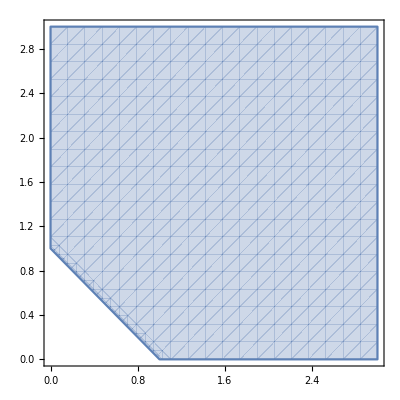

```mathematica
x+y>1&&(1-x)^2+x*y>0
RegionPlot[%,{x,0,3},{y,0,3}]
```

q^++q^->0∧(1-q^-)^2+q^+ q^->0∧1-q^->0

x+y>0∧x y+(1-x)^2>0∧1-x>0

x+y>0∧x y+(1-x)^2>0∧1-x>0∧1/10>y/(1-x)

x+y>0∧x y+(1-x)^2>0∧1-x>0∧1/10>x

x+y>0∧x y+(1-x)^2>0∧1-x>0∧1/10>1-x

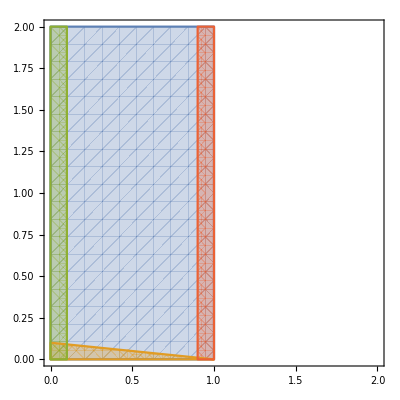

```mathematica
qp+qm>0&&(Q-qm)^2+qp*qm>0&&(Q-qm)>0/.Q->1
reg1=%/.qm->x/.qp->y
reg2=reg1&&tau>y/(1-x)/.tau->1/10
reg3=reg1&&tau>x/.tau->1/10
reg4=reg1&&tau>1-x/.tau->1/10
RegionPlot[{reg1,reg2},{x,0,2},{y,0,2}];
RegionPlot[{reg1,reg3},{x,0,2},{y,0,2}];
RegionPlot[{reg1,reg4},{x,0,2},{y,0,2}];
RegionPlot[{reg1,reg2,reg3,reg4},{x,0,2},{y,0,2}]
```

```mathematica
Tan[I*p1m]
Sin[I*p1m]
Cos[I*p1m]
```

ⅈ tanh(p_1^-)

ⅈ sinh(p_1^-)

cosh(p_1^-)

q^++q^->0∧(1-q^-)^2+q^+ q^->0∧1-q^->0

x+y>0∧x y+(1-x)^2>0∧1-x>0

x+y>0∧x y+(1-x)^2>0∧1-x>0∧1/10>2 √(x y)

x+y>0∧x y+(1-x)^2>0∧1-x>0∧1/10>√(x y)

x+y>0∧x y+(1-x)^2>0∧1-x>0∧1/10>√(x y)

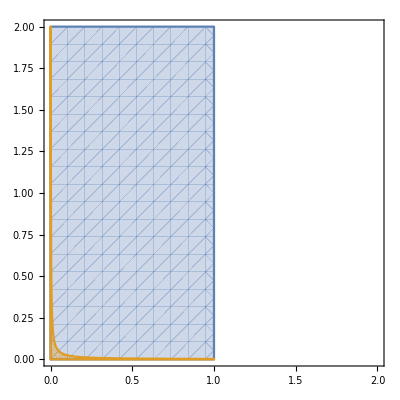

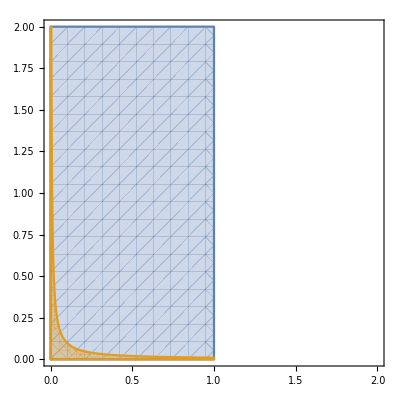

-Graphics-

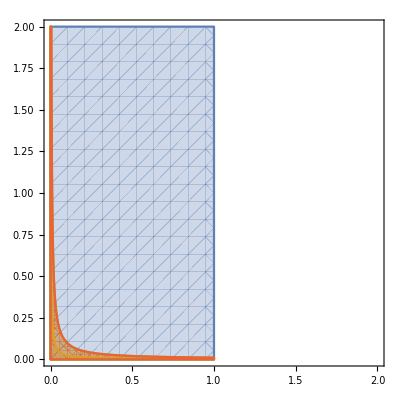

```mathematica
qp+qm>0&&(Q-qm)^2+qp*qm>0&&(Q-qm)>0/.Q->1
reg1=%/.qm->x/.qp->y
reg2=reg1&&tau>2*Sqrt[qp*qm]/.tau->1/10/.qm->x/.qp->y
reg3=reg1&&tau>Sqrt[qp*qm]/.tau->1/10/.qm->x/.qp->y
reg4=reg1&&tau>Sqrt[qp*qm]/.tau->1/10/.qm->x/.qp->y
RegionPlot[{reg1,reg2},{x,0,2},{y,0,2}]
RegionPlot[{reg1,reg3},{x,0,2},{y,0,2}]
RegionPlot[{reg1,reg4},{x,0,2},{y,0,2}]
RegionPlot[{reg1,reg2,reg3,reg4},{x,0,2},{y,0,2}]
```

```mathematica
tauHatA=(p1m)^((1-abar)/2)(p1p)^((1+abar)/2)+(qm)^((1-abar)/2)(qp)^((1+abar)/2)
```

(p_1^+)^((abar+1)/2) (p_1^-)^((1-abar)/2)+(q^+)^((abar+1)/2) (q^-)^((1-abar)/2)

q^++q^->0∧(1-q^-)^2+q^+ q^->0∧-q^+-q^-+1>0

x+y>0∧x y+(1-x)^2>0∧-x-y+1>0

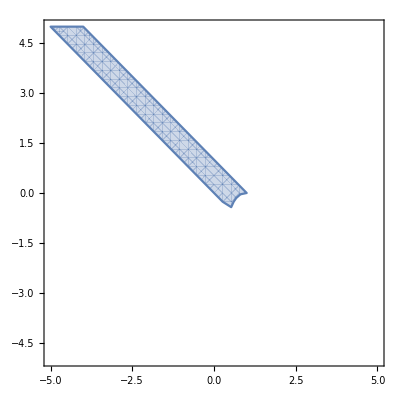

```mathematica
qp+qm>0&&(Q-qm)^2+qp*qm>0&&(Q-qm-qp)>0/.Q->1
reg1=%/.qm->x/.qp->y
RegionPlot[reg1,{x,-5,5},{y,-5,5}]
```

```mathematica
(* n-sector 1-gluon *)

LOsectorWmunuAvgN*onShellDelta*momConsDeltaN*(kp*km)^-eps/8/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0//applyDrellYanNotation//Simplify
%(*/.zerop+I*km->-I(-km+I*zerop)*)/.zerop->0//Simplify

%//applyKsqrDiracDeltaKPlus;
%//applyDiracDeltaKPerp;
%//applyDiracDeltaKMinus;
%/.z1-1->-z1bar/.z2-1->-z2bar/.HeavisideTheta[a_,b_,c_,d_]->1//applyDrellYanNotation//Expand
%/.myDelta[-z2bar*p2p]->myDelta[z2bar]/p2p/.(-z1bar*p1m)^(-a_):> (-p1m+I*zerop)^(-a)(z1bar)^(-a)//Simplify

%/. (z1bar)^(-1-eta1):> (-myDelta[z1bar]/eta1+PlusDistribution[myTheta[z1bar]/z1bar]-eta1*PlusDistribution[myTheta[z1bar]Log[z1bar]/z1bar])
%/. (z1bar)^(-eta1):> z1bar(-myDelta[z1bar]/eta1+PlusDistribution[myTheta[z1bar]/z1bar]-eta1*PlusDistribution[myTheta[z1bar]Log[z1bar]/z1bar])

etaSeriesN=Series[%(*/.zerop->0*),{eta1,0,0}]//Normal
ZnEta=Series[etaSeriesN/.zerop->0,{eta1,0,-1}]//Normal
etaSeriesFiniteN=etaSeriesN-ZnEta//Simplify

%/.muMS^(2eps)(QT^2)^(-1-eps)->-myDelta[QT^2]/eps+MuSqrDistribution[myTheta[QT^2]/QT^2]-eps*MuSqrDistribution[Log[QT^2/muMS^2]myTheta[QT^2]/QT^2]

tripPlusN=%/.myTheta[p1m*z1bar]->myTheta[z1bar]/.myDelta[-z2bar*p2p]->myDelta[z2bar]/p2p/.myDelta[z1bar*p1m]->myDelta[z1bar]/p1m





(* work with eps^0 terms *)
SeriesCoefficient[tripPlusN,{eps,0,0}];
epsNeg0N=%//applyDiracDeltaSimplification//Together



(* work with eps^-1 terms *)
SeriesCoefficient[tripPlusN,{eps,0,-1}];
(* since *)
%/.AP1->PlusDistribution[(1+z1^2)myTheta[z1bar]/z1bar]/.PlusDistribution[(1+z1^2)*myTheta[z1bar]/z1bar]->(1+z1^2)PlusDistribution[myTheta[z1bar]/z1bar]+3*myDelta[z1bar]/2;
(* we do *)
%/.PlusDistribution[myTheta[z1bar]/z1bar]->(AP1-3myDelta[z1bar]/2)/(1+z1^2)/.z1bar^2->2z1bar-1+z1^2//Simplify;

epsNeg1N=%//applyDiracDeltaSimplification//Together

(* work with eps^-2 terms *)
SeriesCoefficient[tripPlusN,{eps,0,-2}];
epsNeg2N=%//applyDiracDeltaSimplification//Together
```

-(p_2^+ ᾱ (k^+ k^-)^-ϵ (-k^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (g^ρτ)_⊥ k^+,k^-,z_2 p_2^+,z_1 p_1^- (ⅈ ((k^-)^2 (ϵ-1) (-k^-+ⅈ 0^+)^η_1+2 k^- p_1^- ν_1^η_1-2 (p_1^-)^2 ν_1^η_1)+0^+ k^- (ϵ-1) (-k^-+ⅈ 0^+)^η_1) δ[k^+ k^-+(k_⊥)^2] δ[p_2^+ (z_2-1)] δ[k^-+p_1^- (z_1-1)] δ[k_⊥+Q_⊥])/(k^+ p_1^- (0^++ⅈ k^-))

-(p_2^+ ᾱ (-k^-)^-η_1 (k^+ k^-)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^ρτ)_⊥ k^+,k^-,z_2 p_2^+,z_1 p_1^- (2 k^- p_1^- ν_1^η_1+(ϵ-1) (-k^-)^(η_1+2)-2 (p_1^-)^2 ν_1^η_1) δ[k^+ k^-+(k_⊥)^2] δ[p_2^+ (z_2-1)] δ[k^-+p_1^- (z_1-1)] δ[k_⊥+Q_⊥])/p_1^-

-2 p_2^+ ᾱ ν_1^η_1 μ_OverBar[MS]^(2 ϵ) (-(z̄)_1 p_1^-)^-η_1 (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[-(z̄)_2 p_2^+]+(2 p_2^+ ᾱ ν_1^η_1 μ_OverBar[MS]^(2 ϵ) (-(z̄)_1 p_1^-)^-η_1 (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[-(z̄)_2 p_2^+])/((z̄)_1)+(z̄)_1 p_2^+ ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[-(z̄)_2 p_2^+]-(z̄)_1 p_2^+ ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[-(z̄)_2 p_2^+]

2 ᾱ ν_1^η_1 (z̄)_1^(-η_1-1) (-p_1^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]-2 ᾱ ν_1^η_1 (z̄)_1^-η_1 (-p_1^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]+(z̄)_1 ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]-(z̄)_1 ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]

2 ᾱ ν_1^η_1 (-p_1^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] (-δ[(z̄)_1]/η_1-η_1 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++(θ[(z̄)_1]/((z̄)_1))_+)-2 ᾱ ν_1^η_1 (z̄)_1^-η_1 (-p_1^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]+(z̄)_1 ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]-(z̄)_1 ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]

2 ᾱ ν_1^η_1 (-p_1^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] (-δ[(z̄)_1]/η_1-η_1 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++(θ[(z̄)_1]/((z̄)_1))_+)-2 (z̄)_1 ᾱ ν_1^η_1 (-p_1^-+ⅈ 0^+)^-η_1 μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] (-δ[(z̄)_1]/η_1-η_1 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++(θ[(z̄)_1]/((z̄)_1))_+)+(z̄)_1 ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]-(z̄)_1 ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2]

(2 ((z̄)_1-1) ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2])/η_1-ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] (2 (z̄)_1 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 (z̄)_1 log(ν_1) δ[(z̄)_1]+2 log(ν_1) δ[(z̄)_1]+2 (z̄)_1 (θ[(z̄)_1]/((z̄)_1))_+-2 (θ[(z̄)_1]/((z̄)_1))_++(z̄)_1 ϵ-(z̄)_1)

(2 ((z̄)_1-1) ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2])/η_1

ᾱ (-μ_OverBar[MS]^(2 ϵ)) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] (2 (z̄)_1 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 (z̄)_1 log(ν_1) δ[(z̄)_1]+2 log(ν_1) δ[(z̄)_1]+2 ((z̄)_1-1) (θ[(z̄)_1]/((z̄)_1))_++(z̄)_1 (ϵ-1))

-ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (2 (z̄)_1 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 (z̄)_1 log(ν_1) δ[(z̄)_1]+2 log(ν_1) δ[(z̄)_1]+2 ((z̄)_1-1) (θ[(z̄)_1]/((z̄)_1))_++(z̄)_1 (ϵ-1)) (-δ[Q_T^2]/ϵ-ϵ ((log(Q_T^2/μ_OverBar[MS]^2) θ[Q_T^2])/Q_T^2)_(μ^2)+(θ[Q_T^2]/Q_T^2)_(μ^2))

-ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (2 (z̄)_1 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 log(-p_1^-+ⅈ 0^+) δ[(z̄)_1]-2 (z̄)_1 log(ν_1) δ[(z̄)_1]+2 log(ν_1) δ[(z̄)_1]+2 ((z̄)_1-1) (θ[(z̄)_1]/((z̄)_1))_++(z̄)_1 (ϵ-1)) (-δ[Q_T^2]/ϵ-ϵ ((log(Q_T^2/μ_OverBar[MS]^2) θ[Q_T^2])/Q_T^2)_(μ^2)+(θ[Q_T^2]/Q_T^2)_(μ^2))

2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)-2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)-2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]

1/(2 (z_1^2+1))(-4 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 z_1^2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+4 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+4 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+4 z_1^2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 (z̄)_1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+3 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])

0

```mathematica
epsNeg1N/.z1bar->1-z1//Expand
%//applyDiracDeltaSimplification
Collect2[%/.z1->1-z1bar,myDelta[_]]//FullSimplify
```

-(2 z_1^2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)-(2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)-(2 AP1 z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)+(2 z_1^2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)+(2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)+(z_1^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)+(3 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(2 (z_1^2+1))+(z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(2 (z_1^2+1))

-(2 z_1^2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)-(2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)-(2 AP1 z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)+(2 z_1^2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)+(2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(z_1^2+1)+(z_1^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)+(3 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(2 (z_1^2+1))+(z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[1-z_1] δ[Q_T^2])/(2 (z_1^2+1))

ᾱ ((2 AP1 ((z̄)_1-1))/(((z̄)_1-2) (z̄)_1+2)-(z̄)_1) (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+1/2 ᾱ (-4 log(-p_1^-+ⅈ 0^+)+4 log(ν_1)+3) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

```mathematica
epsNeg1N+ZnEta
%/.muMS^(2eps)(QT^2)^(-1-eps)->-myDelta[QT^2]/eps+MuSqrDistribution[myTheta[QT^2]/QT^2]-eps*MuSqrDistribution[Log[QT^2/muMS^2]myTheta[QT^2]/QT^2];

%/.myTheta[p1m*z1bar]->myTheta[z1bar]/.myDelta[-z2bar*p2p]->myDelta[z2bar]/p2p/.myDelta[z1bar*p1m]->myDelta[z1bar]/p1m;

Series[%,{eps,0,0}]//Normal;
%//applyDiracDeltaSimplification
```

(2 ((z̄)_1-1) ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2])/η_1+1/(2 (z_1^2+1))(-4 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 z_1^2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+4 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+4 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+4 z_1^2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 (z̄)_1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+3 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])

-2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+(2 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(2 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2))/η_1+2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+3/2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+(2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/(η_1 ϵ)-((z̄)_1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-((z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)

```mathematica
LOsectorWmunuAvgNbar*onShellDelta*momConsDeltaNb(kp*km)^-eps/8/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0//applyDrellYanNotation//Simplify
%/.zerop+I*kp->-I(-kp+I*zerop)//Simplify

%//applyKsqrDiracDeltaKMinus;
%//applyDiracDeltaKPerp;
%//applyDiracDeltaKPlus;
%/.z1-1->-z1bar/.z2-1->-z2bar/.HeavisideTheta[a_,b_,c_,d_]->1//applyDrellYanNotation

%/. (a_*z2bar+b_)^(-1-eta2):> (-myDelta[z2bar]/eta2+PlusDistribution[myTheta[z2bar]/z2bar]-eta2*PlusDistribution[myTheta[z2bar]Log[z2bar]/z2bar])/a

etaSeriesNb=Series[%/.zerop->0,{eta2,0,0}]//Normal
ZnbEta=Series[etaSeriesNb/.zerop->0,{eta2,0,-1}]//Normal
etaSeriesFiniteNb=etaSeriesNb-ZnbEta//Simplify

%/.muMS^(2eps)(QT^2)^(-1-eps)->-myDelta[QT^2]/eps+MuSqrDistribution[myTheta[QT^2]/QT^2]-eps*MuSqrDistribution[Log[QT^2/muMS^2]myTheta[QT^2]/QT^2]

tripPlusNb=%/.myTheta[p2p*z2bar]->myTheta[z2bar]/.myDelta[-z1bar*p1m]->myDelta[z1bar]/p1m/.myDelta[z2bar*p2p]->myDelta[z2bar]/p2p


(* work with eps^0 terms *)
SeriesCoefficient[tripPlusNb,{eps,0,0}];
epsNeg0Nb=%//applyDiracDeltaSimplification//Together


(* work with eps^-1 terms *)
SeriesCoefficient[tripPlusNb,{eps,0,-1}];
(* since *)
%/.AP2->PlusDistribution[(1+z2^2)myTheta[z2bar]/z2bar]/.PlusDistribution[(1+z2^2)*myTheta[z2bar]/z2bar]->(1+z2^2)PlusDistribution[myTheta[z2bar]/z2bar]+3*myDelta[z2bar]/2;
(* we do *)
%/.PlusDistribution[myTheta[z2bar]/z2bar]->(AP2-3myDelta[z2bar]/2)/(1+z2^2)/.z2bar^2->2z2bar-1+z2^2//Simplify;
epsNeg1Nb=%//applyDiracDeltaSimplification//Together


(* work with eps^-2 terms *)
SeriesCoefficient[tripPlusNb,{eps,0,-2}];
epsNeg2Nb=%//applyDiracDeltaSimplification//Together
```

-(p_1^- ᾱ (k^+ k^-)^-ϵ (-k^++ⅈ 0^+)^-η_2 μ_OverBar[MS]^(2 ϵ) (g^ρτ)_⊥ k^+,k^-,z_2 p_2^+,z_1 p_1^- (ⅈ ((k^+)^2 (ϵ-1) (-k^++ⅈ 0^+)^η_2+2 k^+ p_2^+ ν_2^η_2-2 (p_2^+)^2 ν_2^η_2)+0^+ k^+ (ϵ-1) (-k^++ⅈ 0^+)^η_2) δ[k^+ k^-+(k_⊥)^2] δ[p_1^- (z_1-1)] δ[k^++p_2^+ (z_2-1)] δ[k_⊥+Q_⊥])/(k^- p_2^+ (0^++ⅈ k^+))

-(ⅈ p_1^- ᾱ (k^+ k^-)^-ϵ (-k^++ⅈ 0^+)^(-η_2-1) μ_OverBar[MS]^(2 ϵ) (g^ρτ)_⊥ k^+,k^-,z_2 p_2^+,z_1 p_1^- (ⅈ ((k^+)^2 (ϵ-1) (-k^++ⅈ 0^+)^η_2+2 k^+ p_2^+ ν_2^η_2-2 (p_2^+)^2 ν_2^η_2)+0^+ k^+ (ϵ-1) (-k^++ⅈ 0^+)^η_2) δ[k^+ k^-+(k_⊥)^2] δ[p_1^- (z_1-1)] δ[k^++p_2^+ (z_2-1)] δ[k_⊥+Q_⊥])/(k^- p_2^+)

-(ⅈ p_1^- ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (-(z̄)_2 p_2^++ⅈ 0^+)^(-η_2-1) (g^ρτ)_⊥ (ⅈ ((z̄)_2^2 (p_2^+)^2 (ϵ-1) (-(z̄)_2 p_2^++ⅈ 0^+)^η_2+2 (z̄)_2 (p_2^+)^2 ν_2^η_2-2 (p_2^+)^2 ν_2^η_2)+0^+ (z̄)_2 p_2^+ (ϵ-1) (-(z̄)_2 p_2^++ⅈ 0^+)^η_2) δ[-(z̄)_1 p_1^-])/p_2^+

(ⅈ p_1^- ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ (ⅈ ((z̄)_2^2 (p_2^+)^2 (ϵ-1) (-(z̄)_2 p_2^++ⅈ 0^+)^η_2+2 (z̄)_2 (p_2^+)^2 ν_2^η_2-2 (p_2^+)^2 ν_2^η_2)+0^+ (z̄)_2 p_2^+ (ϵ-1) (-(z̄)_2 p_2^++ⅈ 0^+)^η_2) δ[-(z̄)_1 p_1^-] (-δ[(z̄)_2]/η_2-η_2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_++(θ[(z̄)_2]/((z̄)_2))_+))/((p_2^+)^2)

(p_1^- ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[-(z̄)_1 p_1^-] ((2 (z̄)_2 (p_2^+)^2 log(ν_2)+(z̄)_2^2 (ϵ-1) ((p_2^+)^2 log(-(z̄)_2)+(p_2^+)^2 log(p_2^+))-2 (p_2^+)^2 log(ν_2)) δ[(z̄)_2]-((z̄)_2^2 (p_2^+)^2 (ϵ-1)+2 (z̄)_2 (p_2^+)^2-2 (p_2^+)^2) (θ[(z̄)_2]/((z̄)_2))_+))/((p_2^+)^2)+(p_1^- ᾱ ((z̄)_2^2 ϵ-(z̄)_2^2+2 (z̄)_2-2) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] δ[-(z̄)_1 p_1^-])/η_2

(p_1^- ᾱ ((z̄)_2^2 ϵ-(z̄)_2^2+2 (z̄)_2-2) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[(z̄)_2] δ[-(z̄)_1 p_1^-])/η_2

(p_1^- ᾱ μ_OverBar[MS]^(2 ϵ) (Q_T^2)^(-ϵ-1) (g^ρτ)_⊥ δ[-(z̄)_1 p_1^-] ((p_2^+)^2 (2 ((z̄)_2-1) log(ν_2)+(z̄)_2^2 (ϵ-1) log(-(z̄)_2 p_2^+)) δ[(z̄)_2]-(p_2^+)^2 ((z̄)_2^2 (ϵ-1)+2 (z̄)_2-2) (θ[(z̄)_2]/((z̄)_2))_+))/((p_2^+)^2)

(p_1^- ᾱ (g^ρτ)_⊥ δ[-(z̄)_1 p_1^-] ((p_2^+)^2 (2 ((z̄)_2-1) log(ν_2)+(z̄)_2^2 (ϵ-1) log(-(z̄)_2 p_2^+)) δ[(z̄)_2]-(p_2^+)^2 ((z̄)_2^2 (ϵ-1)+2 (z̄)_2-2) (θ[(z̄)_2]/((z̄)_2))_+) (-δ[Q_T^2]/ϵ-ϵ ((log(Q_T^2/μ_OverBar[MS]^2) θ[Q_T^2])/Q_T^2)_(μ^2)+(θ[Q_T^2]/Q_T^2)_(μ^2)))/((p_2^+)^2)

(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((p_2^+)^2 (2 ((z̄)_2-1) log(ν_2)+(z̄)_2^2 (ϵ-1) log(-(z̄)_2 p_2^+)) δ[(z̄)_2]-(p_2^+)^2 ((z̄)_2^2 (ϵ-1)+2 (z̄)_2-2) (θ[(z̄)_2]/((z̄)_2))_+) (-δ[Q_T^2]/ϵ-ϵ ((log(Q_T^2/μ_OverBar[MS]^2) θ[Q_T^2])/Q_T^2)_(μ^2)+(θ[Q_T^2]/Q_T^2)_(μ^2)))/((p_2^+)^2)

(z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]-2 ᾱ log(ν_2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)-2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)

1/2 (-2 AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2]+4 ᾱ log(ν_2) (g^ρτ)_⊥ δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2])

0

```mathematica
LOsectorWmunuAvgOver*onShellDelta*momConsDeltaOver(kp*km)^-eps/8/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%/.p1p->0/.p2m->0/.Vperp[p1]->0/.Vperp[p2]->0//applyDrellYanNotation//Simplify
%/.zerop+I*kp->-I(-kp+I*zerop)/.zerop+I*km->-I(-km+I*zerop)//Simplify

%//applyKsqrDiracDeltaKPlus;
%//applyDiracDeltaKPerp;

tester=%/.z1-1->-z1bar/.z2-1->-z2bar/.HeavisideTheta[a_,b_,c_,d_]->1//applyDrellYanNotation


(*Integrate[%,{km,0,Infinity},Assumptions->0<eta<delta3<1&&0<eta<delta4<1&&QT>0]//Simplify;

test=%/.-QT^2+(delta3+I*eta)(delta4+I*eta)->-QT^2/.-2QT^2+2(delta3+I*eta)(delta4+I*eta)->-2QT^2

Limit[%,eta->0]/.Log[delta4]-Log[delta3^2delta4^3]+4Log[QT]->2Log[QT^2/(delta3*delta4)];



%/.Log[QT^2/(delta3*delta4)]->Log[QT^2/muMS^2]+Log[muMS^2/(delta3*delta4)]//Expand

(*%/.Log[muMS^2/(delta3*delta4)]->Log[muMS^2/(-delta3^2-I*eta)]/2+Log[muMS^2/(-delta4^2-I*eta)]/2-2*Pi*I*)
%/.Log[QT]->Log[QT^2/muMS^2]/2+Log[muMS]//Expand

%/.(muMS/QT)^(2eps)Log[QT^2/muMS^2]/QT^2->-myDelta[QT^2]/eps^2+MuSqrDistribution[Log[QT^2/muMS^2]myTheta[QT^2]/QT^2]

%/.(muMS/QT)^(2eps)/QT^2->-myDelta[QT^2]/eps+MuSqrDistribution[myTheta[QT^2]/QT^2]-eps*MuSqrDistribution[Log[QT^2/muMS^2]myTheta[QT^2]/QT^2];

tripPlusOver=%/.myTheta[p2p*z2bar]->myTheta[z2bar]/.myDelta[-z1bar*p1m]->myDelta[z1bar]/p1m/.myDelta[-z2bar*p2p]->myDelta[z2bar]/p2p



(* work with eps^0 terms *)
SeriesCoefficient[tripPlusOver,{eps,0,0}];
epsNeg0Over=%//Together

(* work with eps^-1 terms *)
SeriesCoefficient[tripPlusOver,{eps,0,-1}];
epsNeg1Over=%//Together

(* work with eps^-2 terms *)
SeriesCoefficient[tripPlusOver,{eps,0,-2}];
epsNeg2Over=%//Together*)
```

-(2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (k^+ k^-)^-ϵ (-k^++ⅈ 0^+)^-η_4 (-k^-+ⅈ 0^+)^-η_3 μ_OverBar[MS]^(2 ϵ) (g^ρτ)_⊥ k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] δ[p_2^+ (z_2-1)] δ[p_1^- (z_1-1)] δ[k_⊥+Q_⊥])/((0^++ⅈ k^+) (0^++ⅈ k^-))

2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (k^+ k^-)^-ϵ (-k^++ⅈ 0^+)^(-η_4-1) (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (g^ρτ)_⊥ k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] δ[p_2^+ (z_2-1)] δ[p_1^- (z_1-1)] δ[k_⊥+Q_⊥]

(2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (g^ρτ)_⊥ (-Q_T^2/k^-+ⅈ 0^+)^(-η_4-1) δ[-(z̄)_2 p_2^+] δ[-(z̄)_1 p_1^-])/k^-

```mathematica
tester//Expand
%/.myDelta[_]->1/.Vperp[MTD[_,_]]->1
%/.(-QT^2/km+I*zerop)^(-eta4-1)/km->km^eta4/(-QT^2+I*zerop*km)^(1+eta4)
%/.I*zerop*km->0/.zerop->0/.eta4->eta3//Simplify
low=Integrate[%,{km,0,p3m}]
```

(2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (g^ρτ)_⊥ (-Q_T^2/k^-+ⅈ 0^+)^(-η_4-1) δ[-(z̄)_2 p_2^+] δ[-(z̄)_1 p_1^-])/k^-

(2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (-Q_T^2/k^-+ⅈ 0^+)^(-η_4-1))/k^-

2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (k^-)^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (-Q_T^2+ⅈ 0^+ k^-)^(-η_4-1)

2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_3 (-k^-)^(-η_3-1) (k^-)^η_3 μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η_3-1) (Q_T^2)^-ϵ

Integrate::idiv: Integral of 2 (TraditionalForm`μ)_OverBar[MS]^(2 ϵ) ν_3^η_3 ν_4^η_3 (-Q_T^2)^(-1-η_3) (Q_T^2)^-ϵ ᾱ (-k^-)^(-1-η_3) (k^-)^η_3 p_2^+ p_1^-
 does not converge on {0,p_3^-}.

∫_0^(p_3^-) 2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_3 (-k^-)^(-η_3-1) (k^-)^η_3 μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η_3-1) (Q_T^2)^-ϵⅆ k^-

```mathematica
tester//Expand
%/.myDelta[_]->1/.Vperp[MTD[_,_]]->1
%/.(-QT^2/km+I*zerop)^(-eta4-1)/km->km^eta4/(-QT^2+I*zerop*km)^(1+eta4)
%/.I*zerop*km->0/.zerop->0/.eta3->eta/.eta4->eta
high=Integrate[%,{km,p2m,Infinity}]
```

(2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (g^ρτ)_⊥ (-Q_T^2/k^-+ⅈ 0^+)^(-η_4-1) δ[-(z̄)_2 p_2^+] δ[-(z̄)_1 p_1^-])/k^-

(2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (-Q_T^2/k^-+ⅈ 0^+)^(-η_4-1))/k^-

2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_4 (k^-)^η_4 (-k^-+ⅈ 0^+)^(-η_3-1) μ_OverBar[MS]^(2 ϵ) (Q_T^2)^-ϵ (-Q_T^2+ⅈ 0^+ k^-)^(-η_4-1)

2 p_2^+ p_1^- ᾱ ν_3^η ν_4^η (-k^-)^(-η-1) (k^-)^η μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η-1) (Q_T^2)^-ϵ

Integrate::idiv: Integral of (2 (-1)^-η (TraditionalForm`μ)_OverBar[MS]^(2 ϵ) ν_3^η ν_4^η (-Q_T^2)^-η (Q_T^2)^-ϵ ᾱ p_2^+ p_1^-)/(Q_T^2 k^-)
 does not converge on {p_2^-,∞}.

∫_(p_2^-)^∞ 2 p_2^+ p_1^- ᾱ ν_3^η ν_4^η (-k^-)^(-η-1) (k^-)^η μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η-1) (Q_T^2)^-ϵⅆ k^-

```mathematica
(Normal[low])+(Normal[high])
Series[%,{zerop,0,0}]//Normal
%//Simplify
```

∫_(p_2^-)^∞ 2 p_2^+ p_1^- ᾱ ν_3^η ν_4^η (-k^-)^(-η-1) (k^-)^η μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η-1) (Q_T^2)^-ϵⅆ k^-+∫_0^(p_3^-) 2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_3 (-k^-)^(-η_3-1) (k^-)^η_3 μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η_3-1) (Q_T^2)^-ϵⅆ k^-

Integrate[2 p_2^+ p_1^- ᾱ ν_3^η ν_4^η (-k^-)^(-η-1) (k^-)^η μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η-1) (Q_T^2)^-ϵ,{k^-,p_2^-,∞},Assumptions→μ_OverBar[MS]>0∧s>0∧ϵ>0∧ᾱ>0∧0^+>0∧p_1^+>0∧p_2^+>0∧p_1^->0∧p_2^->0∧0<z_1<1∧0<z_2<1∧0<δ<1]+Integrate[2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_3 (-k^-)^(-η_3-1) (k^-)^η_3 μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η_3-1) (Q_T^2)^-ϵ,{k^-,0,p_3^-},Assumptions→μ_OverBar[MS]>0∧s>0∧ϵ>0∧ᾱ>0∧0^+>0∧p_1^+>0∧p_2^+>0∧p_1^->0∧p_2^->0∧0<z_1<1∧0<z_2<1∧0<δ<1]

Integrate[2 p_2^+ p_1^- ᾱ ν_3^η ν_4^η (-k^-)^(-η-1) (k^-)^η μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η-1) (Q_T^2)^-ϵ,{k^-,p_2^-,∞},Assumptions→True]+Integrate[2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_3 (-k^-)^(-η_3-1) (k^-)^η_3 μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η_3-1) (Q_T^2)^-ϵ,{k^-,0,p_3^-},Assumptions→True]

```mathematica
Series[%,{zerop,0,0}]//Normal
```

Integrate[2 p_2^+ p_1^- ᾱ ν_3^η ν_4^η (-k^-)^(-η-1) (k^-)^η μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η-1) (Q_T^2)^-ϵ,{k^-,p_2^-,∞},Assumptions→μ_OverBar[MS]>0∧s>0∧ϵ>0∧ᾱ>0∧0^+>0∧p_1^+>0∧p_2^+>0∧p_1^->0∧p_2^->0∧0<z_1<1∧0<z_2<1∧0<δ<1]+Integrate[2 p_2^+ p_1^- ᾱ ν_3^η_3 ν_4^η_3 (-k^-)^(-η_3-1) (k^-)^η_3 μ_OverBar[MS]^(2 ϵ) (-Q_T^2)^(-η_3-1) (Q_T^2)^-ϵ,{k^-,0,p_3^-},Assumptions→μ_OverBar[MS]>0∧s>0∧ϵ>0∧ᾱ>0∧0^+>0∧p_1^+>0∧p_2^+>0∧p_1^->0∧p_2^->0∧0<z_1<1∧0<z_2<1∧0<δ<1]

#### Results

```mathematica
(* 0-gluons + virtual corrections gives *)
virtual=epsNeg00g+epsNeg10g/eps+epsNeg20g/eps^2//applyDrellYanNotation
```

(-4 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+4 ᾱ log(ν) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-(2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

```mathematica
(* 1-gluon eps^-2 result *)

realEpsNeg2=(epsNeg2N+epsNeg2Nb-epsNeg2Over)/eps^2
```

-epsNeg2Over/ϵ^2

```mathematica
(* 1-gluon ps^-1 result *)

epsNeg1N+epsNeg1Nb-epsNeg1Over/.LFF1->Log[delta1/p1m]-I*Pi/.LFF2->Log[delta2/p2p]
%//expLogs//Expand;
%//applyDiracDeltaSimplification;
Collect2[%,myDelta[_]];
%/.Log[p2p]->Log[(-p2p*p1m-I*delta)*delta3*delta4/(muMS^2*delta1*delta2)]+I*Pi-Log[p1m]-Log[delta3]-Log[delta4]+2Log[muMS]+Log[delta1]+Log[delta2]//Expand;

(*%/.delta1*delta2->(-p1m*p2p-I*delta)/(nu^2*delta3*delta4)*)
realEpsNeg1=%/eps/. 1/(delta1*delta2)->nu^2/((-p1m*p2p-I*delta)*delta3*delta4)
```

1/(2 (z_1^2+1))(-4 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 z_1^2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+4 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+4 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+4 z_1^2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 (z̄)_1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]+3 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])+1/2 (-2 AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2]+4 ᾱ log(ν_2) (g^ρτ)_⊥ δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[(z̄)_1] δ[Q_T^2])-epsNeg1Over

(-2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+(2 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(2 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2]+2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+2 ᾱ log(ν_2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-((z̄)_1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-((z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-epsNeg1Over)/ϵ

```mathematica
(* 1-gluon eps^-0 result *)

epsNeg0N+epsNeg0Nb-epsNeg0Over/.LFF1->Log[delta1/p1m]-I*Pi/.LFF2->Log[delta2/p2p];
%//expLogs//Expand;
%//applyDiracDeltaSimplification;
Collect2[%,myDelta[_]]
%/.Log[p2p]->Log[(-p2p*p1m-I*delta)*delta3*delta4/(muMS^2*delta1*delta2)]+I*Pi-Log[p1m]-Log[delta3]-Log[delta4]+2Log[muMS]+Log[delta1]+Log[delta2]//Expand;

(*%/.delta1*delta2->(-p1m*p2p-I*delta)/(nu^2*delta3*delta4)*)
%/. 1/(delta1*delta2)->nu^2/((-p1m*p2p-I*delta)*delta3*delta4);
Collect2[%,myDelta[_]]/. z2bar^2-2z2bar+2->1+z2^2/. z1bar^2-2z1bar+2->1+z1^2;
realEpsNeg0=%/.Log[nu^2/muMS^2]MuSqrDistribution[myTheta[QT^2]/QT^2]->MuSqrDistribution[Log[nu^2/QT^2]myTheta[QT^2]/QT^2]+MuSqrDistribution[(2Log[QT]-2Log[muMS])myTheta[QT^2]/QT^2]
(*%/.z2bar^2->2z2bar-1+z2^2/.z1bar^2->2z1bar-1+z1^2//Expand;
Collect2[%,myDelta[_]]*)
```

-2 ᾱ (-log(-p_1^-+ⅈ 0^+)+log(ν_1)+log(ν_2)) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]+((z̄)_2^2-2 (z̄)_2+2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)-ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (2 (z̄)_1 (θ[(z̄)_1]/((z̄)_1))_+-2 (θ[(z̄)_1]/((z̄)_1))_+-(z̄)_1) (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]-epsNeg0Over

-2 ᾱ (-log(-p_1^-+ⅈ 0^+)+log(ν_1)+log(ν_2)) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]-ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (2 (z̄)_1 (θ[(z̄)_1]/((z̄)_1))_+-2 (θ[(z̄)_1]/((z̄)_1))_+-(z̄)_1) (θ[Q_T^2]/Q_T^2)_(μ^2)+(z_2^2+1) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]-epsNeg0Over

```mathematica
totalRealVirtual=virtual+realEpsNeg0+realEpsNeg1+realEpsNeg2//expLogs//Expand
```

2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)-(2 ᾱ log(-p_1^-+ⅈ 0^+) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+(2 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/((z_1^2+1) ϵ)-(2 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/((z_1^2+1) ϵ)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2])/ϵ+(z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2]-2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)-2 ᾱ log(ν_2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[Q_T^2]/Q_T^2)_(μ^2)-2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ (θ[Q_T^2]/Q_T^2)_(μ^2)-(4 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]-(2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ^2+(2 ᾱ log(ν_1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+(2 ᾱ log(ν_2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ+(4 ᾱ log(ν) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])/ϵ-((z̄)_1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/((z_1^2+1) ϵ)-((z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/((z_1^2+1) ϵ)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-epsNeg0Over-epsNeg1Over/ϵ-epsNeg2Over/ϵ^2

```mathematica
(* momentum conservation with lightcone components *)

ff[qp,qm,Vperp[q]]
Integrate[%*2DiracDelta[qp-p1p-p2p]DiracDelta[qm-p1m-p2m]DiracDelta[Vperp[q]-Vperp[p1]-Vperp[p2]],{Vperp[q],-Infinity,Infinity},Assumptions->Vperp[p1]>0&&Vperp[p2]>0]/2
Integrate[%,{qm,-Infinity,Infinity},Assumptions->p1m>0&&p2m>0]
Integrate[%,{qp,-Infinity,Infinity},Assumptions->p1p>0&&p2p>0]
```

ff(q^+,q^-,q_⊥)

p_1^++p_2^+-q^+ p_1^-+p_2^--q^- ff(q^+,q^-,p_1_⊥+p_2_⊥)

p_1^++p_2^+-q^+ ff(q^+,p_1^-+p_2^-,p_1_⊥+p_2_⊥)

ff(p_1^++p_2^+,p_1^-+p_2^-,p_1_⊥+p_2_⊥)

```mathematica
(* momentum conservation with Q^2 and Y  *)

ff[SPD[Q,n],SPD[Q,nb],Vperp[Q]]
%*2myFunc[Log[SPD[nb,Q]/SPD[n,Q]]/2-Log[(p1m+p2m)/(p1p+p2p)]/2]myDelta[SPD[Q]-SPD[p1+p2]]DiracDelta[Vperp[Q]-Vperp[p1]-Vperp[p2]]//lcCompAll
Integrate[%,{Vperp[Q],-Infinity,Infinity},Assumptions->Vperp[p1]>0&&Vperp[p2]>0]/2
%//Activate

Integrate[%,{SPD[nb,Q],-Infinity,Infinity},Assumptions->p1m>0&&p2m>0&&SPD[n,Q]>0]
%/.myFunc[a_]:>DiracDelta[a]

Integrate[%,{SPD[n,Q],-Infinity,Infinity},Assumptions->p1p>0&&p2p>0]
```

ff(Q^+,Q^-,Q_⊥)

2 ff(Q^+,Q^-,Q_⊥) p_1_⊥+p_2_⊥-Q_⊥ myFunc(1/2 log(Q^-/Q^+)-1/2 log((p_1^-+p_2^-)/(p_1^++p_2^+))) δ[-2 (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+Q^+ Q^-+(Q_⊥)^2]

myFunc(1/2 (log(Q^-/Q^+)-log((p_1^-+p_2^-)/(p_1^++p_2^+)))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥) δ[Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-)]

Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-) myFunc(1/2 (log(Q^-/Q^+)-log((p_1^-+p_2^-)/(p_1^++p_2^+)))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥)

(myFunc(log((p_1^++p_2^+)/Q^+)) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

(log((p_1^++p_2^+)/Q^+) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

ff(p_1^++p_2^+,p_1^-+p_2^-,p_1_⊥+p_2_⊥)

```mathematica
(* momentum conservation with Q^2 and Y=(Yn+Ynb)/2  *)

ff[SPD[Q,n],SPD[Q,nb],Vperp[Q]]
%*2myFunc[Log[SPD[nb,Q]/SPD[n,Q]]/2-Log[(p1m)/(p1p)]/4-Log[(p2m)/(p2p)]/4]myDelta[SPD[Q]-SPD[p1+p2]]DiracDelta[Vperp[Q]-Vperp[p1]-Vperp[p2]]//lcCompAll
Integrate[%,{Vperp[Q],-Infinity,Infinity},Assumptions->Vperp[p1]>0&&Vperp[p2]>0]/2
%//Activate

Integrate[%,{SPD[nb,Q],-Infinity,Infinity},Assumptions->p1m>0&&p2m>0&&SPD[n,Q]>0]
%/.myFunc[a_]:>DiracDelta[a]//FullSimplify

Integrate[%,{SPD[n,Q],-Infinity,Infinity},Assumptions->p1p>0&&p2p>0&&p1m>0&&p2m>0]
%/.p2m->p1m*p1p/p2p//Simplify
%/.ff[a_,b_,c_]:> ff[a,b/.p1p->p2m*p2p/p1m,c]//Simplify
```

ff(Q^+,Q^-,Q_⊥)

2 ff(Q^+,Q^-,Q_⊥) p_1_⊥+p_2_⊥-Q_⊥ myFunc(-1/4 log(p_1^-/p_1^+)-1/4 log(p_2^-/p_2^+)+1/2 log(Q^-/Q^+)) δ[-2 (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+Q^+ Q^-+(Q_⊥)^2]

myFunc(1/4 (-log(p_1^-/p_1^+)-log(p_2^-/p_2^+)+2 log(Q^-/Q^+))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥) δ[Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-)]

Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-) myFunc(1/4 (-log(p_1^-/p_1^+)-log(p_2^-/p_2^+)+2 log(Q^-/Q^+))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥)

(myFunc(1/4 (2 log(p_1^++p_2^+)+log((p_1^+ p_2^+)/(p_1^- p_2^-))+2 log(p_1^-+p_2^-)-4 log(Q^+))) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

(4 log(p_1^+)+log(p_2^+)-4 log(Q^+)-log(p_1^- p_2^-)+2 log((p_1^++p_2^+) (p_1^-+p_2^-)) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

ff(((p_1^+ p_2^+)/(p_1^- p_2^-))^(1/4) √((p_1^++p_2^+) (p_1^-+p_2^-)),((p_1^- p_2^-)/(p_1^+ p_2^+))^(1/4) √((p_1^++p_2^+) (p_1^-+p_2^-)),p_1_⊥+p_2_⊥)

ff(p_1^++p_2^+,((p_1^++p_2^+) p_1^-)/p_2^+,p_1_⊥+p_2_⊥)

ff(p_1^++p_2^+,p_1^-+p_2^-,p_1_⊥+p_2_⊥)

```mathematica
(* momentum conservation with Q^2 and 2Y=Log[p1m/p2p]  *)

ff[SPD[Q,n],SPD[Q,nb],Vperp[Q]]
%*2myFunc[Log[SPD[nb,Q]/SPD[n,Q]]/2-Log[(p1m)/(p2p)]/2]myDelta[SPD[Q]-SPD[p1+p2]]DiracDelta[Vperp[Q]-Vperp[p1]-Vperp[p2]]//lcCompAll
Integrate[%,{Vperp[Q],-Infinity,Infinity},Assumptions->Vperp[p1]>0&&Vperp[p2]>0]/2
%//Activate

Integrate[%,{SPD[nb,Q],-Infinity,Infinity},Assumptions->p1m>0&&p2m>0&&SPD[n,Q]>0]
%/.myFunc[a_]:>DiracDelta[a]//FullSimplify

Integrate[%,{SPD[n,Q],-Infinity,Infinity},Assumptions->p1p>0&&p2p>0&&p1m>0&&p2m>0]

%//FullSimplify
```

ff(Q^+,Q^-,Q_⊥)

2 ff(Q^+,Q^-,Q_⊥) p_1_⊥+p_2_⊥-Q_⊥ myFunc(1/2 log(Q^-/Q^+)-1/2 log(p_1^-/p_2^+)) δ[-2 (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+Q^+ Q^-+(Q_⊥)^2]

myFunc(1/2 (log(Q^-/Q^+)-log(p_1^-/p_2^+))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥) δ[Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-)]

Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-) myFunc(1/2 (log(Q^-/Q^+)-log(p_1^-/p_2^+))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥)

(myFunc(1/2 (log((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-)-2 log(Q^+))) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

(2 2 log(Q^+)-log((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

ff(√((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-),√(((p_1^++p_2^+) p_1^- (p_1^-+p_2^-))/p_2^+),p_1_⊥+p_2_⊥)

ff(√((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-),√(((p_1^++p_2^+) p_1^- (p_1^-+p_2^-))/p_2^+),p_1_⊥+p_2_⊥)

```mathematica
(* momentum conservation with Q^2 and 2Y=Log[p1m/p2p]  *)

ff[SPD[Q,n],SPD[Q,nb],Vperp[Q]]
%*2myFunc[Log[SPD[nb,Q]/SPD[n,Q]]/2-Log[(p1m)/(p2p)]/2]myDelta[SPD[Q]-SPD[p1+p2]]DiracDelta[Vperp[Q]-Vperp[p1]-Vperp[p2]]//lcCompAll
Integrate[%,{Vperp[Q],-Infinity,Infinity},Assumptions->Vperp[p1]>0&&Vperp[p2]>0]/2
%//Activate

Integrate[%,{SPD[nb,Q],-Infinity,Infinity},Assumptions->p1m>0&&p2m>0&&SPD[n,Q]>0]
%/.myFunc[a_]:>DiracDelta[a]//FullSimplify

Integrate[%,{SPD[n,Q],-Infinity,Infinity},Assumptions->p1p>0&&p2p>0&&p1m>0&&p2m>0]

%//FullSimplify
```

ff(Q^+,Q^-,Q_⊥)

2 ff(Q^+,Q^-,Q_⊥) p_1_⊥+p_2_⊥-Q_⊥ myFunc(1/2 log(Q^-/Q^+)-1/2 log(p_1^-/p_2^+)) δ[-2 (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+Q^+ Q^-+(Q_⊥)^2]

myFunc(1/2 (log(Q^-/Q^+)-log(p_1^-/p_2^+))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥) δ[Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-)]

Q^+ Q^--(p_1^++p_2^+) (p_1^-+p_2^-) myFunc(1/2 (log(Q^-/Q^+)-log(p_1^-/p_2^+))) ff(Q^+,Q^-,p_1_⊥+p_2_⊥)

(myFunc(1/2 (log((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-)-2 log(Q^+))) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

(2 2 log(Q^+)-log((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-) ff(Q^+,((p_1^++p_2^+) (p_1^-+p_2^-))/Q^+,p_1_⊥+p_2_⊥))/Q^+

ff(√((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-),√(((p_1^++p_2^+) p_1^- (p_1^-+p_2^-))/p_2^+),p_1_⊥+p_2_⊥)

ff(√((p_2^+ (p_1^++p_2^+) (p_1^-+p_2^-))/p_1^-),√(((p_1^++p_2^+) p_1^- (p_1^-+p_2^-))/p_2^+),p_1_⊥+p_2_⊥)

```mathematica
Exp[-2/eps^2]
Series[%,{eps,0,5}]//Normal
```

ⅇ^(-2/ϵ^2)

ⅇ^(-2/ϵ^2)